```mathematica
bpm = 60;
quarter = 60/bpm;
half=2*quarter;
whole=4*quarter;
eighth=1/2*quarter;
sixteenth=1/4*quarter;
dottedHalf=3*quarter;
dottedQuarter=3*eighth;
```

## Adagio - Pathetique Sonata, Beethoven

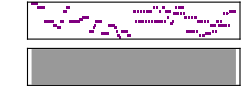

```mathematica
trebleClef=Sound[
{
(* measure 1 *)
SoundNote[{"E5"},half],SoundNote[{"D5"},half],
(* measure 2 *)
SoundNote[{"G4"},dottedHalf],SoundNote[{"F4"},quarter],
(* measure 3 *)
SoundNote[{"E4"},quarter],SoundNote[{"G4"},quarter],SoundNote[{"C5"},quarter],SoundNote[{"D5"},quarter],
(* measure 4 *)
SoundNote[{"G4"},dottedHalf],SoundNote[{"G#4"},quarter],
(* measure 5 *)
SoundNote[{"A4"},half],SoundNote[{"D4"},dottedQuarter],SoundNote[{"E4"},sixteenth],SoundNote[{"F4"},sixteenth],
(* measure 6 *)
SoundNote[{"G4"},half],SoundNote[{"C#4"},half],
(* measure 7 *)
SoundNote[{"F4"},half],SoundNote[{"E4"},eighth],SoundNote[{"D4"},eighth],SoundNote[{"C4"},eighth],SoundNote[{"B3"},eighth],
(* measure 8 *)
SoundNote[{"D4"},half],SoundNote[{"C4"},quarter],SoundNote[{},quarter],
(* measure 9 *)
SoundNote[{"C5"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"C5"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"C5"}, eighth],SoundNote[{"G4"}, eighth],
SoundNote[{"C5"}, eighth],SoundNote[{"G4"}, eighth],
(* measure 10 *)
SoundNote[{"C5"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"C5"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"D5"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"D5"}, eighth],SoundNote[{"G4"}, eighth],
(* measure 11 *)
SoundNote[{"C5"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"D5"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"C5"}, eighth],SoundNote[{"A4"}, eighth],SoundNote[{"C5"}, eighth],SoundNote[{"F#4"}, eighth],
(* measure 12 *)
SoundNote[{"G4"}, eighth],SoundNote[{"B4"}, eighth],SoundNote[{"D5"}, eighth],SoundNote[{"B4"}, eighth],SoundNote[{"D5"}, eighth],SoundNote[{"B4"}, eighth],SoundNote[{"D5"}, eighth],SoundNote[{"B4"}, eighth],
(* measure 13 *)
SoundNote[{"A4"}, eighth],SoundNote[{"D4"}, eighth],SoundNote[{"A4"}, eighth],SoundNote[{"D4"}, eighth],SoundNote[{"A4"}, eighth],SoundNote[{"D4"}, eighth],SoundNote[{"A4"}, eighth],SoundNote[{"D4"}, eighth],
(* measure 14 *)
SoundNote[{"G4"}, eighth],SoundNote[{"C4"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"C4"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"C#4"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"C#4"}, eighth],
(* measure 15 *)
SoundNote[{"F4"}, eighth],SoundNote[{"D4"}, eighth],SoundNote[{"F4"}, eighth],SoundNote[{"D4"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"F4"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"F4"}, eighth],
(* measure 16 *)
SoundNote[{"B4"}, eighth],SoundNote[{"F4"}, eighth],SoundNote[{"B4"}, eighth],SoundNote[{"F4"}, eighth],SoundNote[{"C5"}, half]
}
]
```

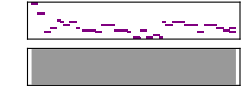

```mathematica
bassClef= Sound[
{
(* measure 1 *)
SoundNote[{"C5"},half],SoundNote[{"F4"},half],
(* measure 2 *)
SoundNote[{"E3"},half],SoundNote[{"G3"},half],
(* measure 3 *)
SoundNote[{"C4"},quarter],SoundNote[{"B3"},quarter],SoundNote[{"A3"},half],
(* measure 4 *)
SoundNote[{"B3"}, half],SoundNote[{"G3"}, quarter],SoundNote[{}, quarter],
(* measure 5 *)
SoundNote[{"F3"}, half],SoundNote[{"F3"}, half],
(* measure 6 *)
SoundNote[{"E3"}, half],SoundNote[{"A3"}, half],
(* measure 7 *)
SoundNote[{"A3"}, half],SoundNote[{"F3"}, half],
(* measure 8 *)
SoundNote[{"F3"}, half],SoundNote[{"E3"}, quarter],SoundNote[{},quarter],
(* measure 9 *)
SoundNote[{"C3"}, half],SoundNote[{"F3"}, half],
(* measure 10 *)
SoundNote[{"C3"}, half],SoundNote[{"D3"}, half],
(* measure 11 *)
SoundNote[{"C3"}, quarter],SoundNote[{"B3"}, quarter],SoundNote[{"A3"}, quarter],SoundNote[{"A3"}, quarter],
(* measure 12 *)
SoundNote[{"B3"}, whole],
(* measure 13 *)
SoundNote[{"A3"}, half],SoundNote[{"A3"}, half],
(* measure 14 *)
SoundNote[{"E3"}, half],SoundNote[{"A3"}, half],
(* measure 15 *)
SoundNote[{"A3"},half],SoundNote[{"G3"},half],
(* measure 16 *)
SoundNote[{"F3"}, half],SoundNote[{"G3","E3"}, half]
}
]
```

## Play: Adagio - Pathetique Sonata

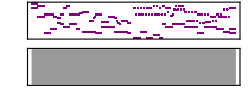

```mathematica
Sound[{Sound[trebleClef,{0,whole*16}],Sound[bassClef, {0,whole*16}]}]
```

```mathematica
Clear[dataTreble];
dataTreble = 
{
(* measure 1 *)
SoundNote[{"E5"},half],SoundNote[{"D5"},half],
(* measure 2 *)
SoundNote[{"G4"},dottedHalf],SoundNote[{"F4"},quarter],
(* measure 3 *)
SoundNote[{"E4"},quarter],SoundNote[{"G4"},quarter],SoundNote[{"C5"},quarter],SoundNote[{"D5"},quarter],
(* measure 4 *)
SoundNote[{"G4"},dottedHalf],SoundNote[{"G#4"},quarter],
(* measure 5 *)
SoundNote[{"A4"},half],SoundNote[{"D4"},dottedQuarter],SoundNote[{"E4"},sixteenth],SoundNote[{"F4"},sixteenth],
(* measure 6 *)
SoundNote[{"G4"},half],SoundNote[{"C#4"},half],
(* measure 7 *)
SoundNote[{"F4"},half],SoundNote[{"E4"},eighth],SoundNote[{"D4"},eighth],SoundNote[{"C4"},eighth],SoundNote[{"B3"},eighth],
(* measure 8 *)
SoundNote[{"D4"},half],SoundNote[{"C4"},quarter],SoundNote[{},quarter],
(* measure 9 *)
SoundNote[{"C5"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"C5"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"C5"}, eighth],SoundNote[{"G4"}, eighth],
SoundNote[{"C5"}, eighth],SoundNote[{"G4"}, eighth],
(* measure 10 *)
SoundNote[{"C5"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"C5"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"D5"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"D5"}, eighth],SoundNote[{"G4"}, eighth],
(* measure 11 *)
SoundNote[{"C5"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"D5"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"C5"}, eighth],SoundNote[{"A4"}, eighth],SoundNote[{"C5"}, eighth],SoundNote[{"F#4"}, eighth],
(* measure 12 *)
SoundNote[{"G4"}, eighth],SoundNote[{"B4"}, eighth],SoundNote[{"D5"}, eighth],SoundNote[{"B4"}, eighth],SoundNote[{"D5"}, eighth],SoundNote[{"B4"}, eighth],SoundNote[{"D5"}, eighth],SoundNote[{"B4"}, eighth],
(* measure 13 *)
SoundNote[{"A4"}, eighth],SoundNote[{"D4"}, eighth],SoundNote[{"A4"}, eighth],SoundNote[{"D4"}, eighth],SoundNote[{"A4"}, eighth],SoundNote[{"D4"}, eighth],SoundNote[{"A4"}, eighth],SoundNote[{"D4"}, eighth],
(* measure 14 *)
SoundNote[{"G4"}, eighth],SoundNote[{"C4"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"C4"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"C#4"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"C#4"}, eighth],
(* measure 15 *)
SoundNote[{"F4"}, eighth],SoundNote[{"D4"}, eighth],SoundNote[{"F4"}, eighth],SoundNote[{"D4"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"F4"}, eighth],SoundNote[{"G4"}, eighth],SoundNote[{"F4"}, eighth],
(* measure 16 *)
SoundNote[{"B4"}, eighth],SoundNote[{"F4"}, eighth],SoundNote[{"B4"}, eighth],SoundNote[{"F4"}, eighth],SoundNote[{"C5"}, half]
};
```

```mathematica
Clear[dataBass];
dataBass =
{
(* measure 1 *)
SoundNote[{"C5"},half],SoundNote[{"F4"},half],
(* measure 2 *)
SoundNote[{"E3"},half],SoundNote[{"G3"},half],
(* measure 3 *)
SoundNote[{"C4"},quarter],SoundNote[{"B3"},quarter],SoundNote[{"A3"},half],
(* measure 4 *)
SoundNote[{"B3"}, half],SoundNote[{"G3"}, quarter],SoundNote[{}, quarter],
(* measure 5 *)
SoundNote[{"F3"}, half],SoundNote[{"F3"}, half],
(* measure 6 *)
SoundNote[{"E3"}, half],SoundNote[{"A3"}, half],
(* measure 7 *)
SoundNote[{"A3"}, half],SoundNote[{"F3"}, half],
(* measure 8 *)
SoundNote[{"F3"}, half],SoundNote[{"E3"}, quarter],SoundNote[{},quarter],
(* measure 9 *)
SoundNote[{"C3"}, half],SoundNote[{"F3"}, half],
(* measure 10 *)
SoundNote[{"C3"}, half],SoundNote[{"D3"}, half],
(* measure 11 *)
SoundNote[{"C3"}, quarter],SoundNote[{"B3"}, quarter],SoundNote[{"A3"}, quarter],SoundNote[{"A3"}, quarter],
(* measure 12 *)
SoundNote[{"B3"}, whole],
(* measure 13 *)
SoundNote[{"A3"}, half],SoundNote[{"A3"}, half],
(* measure 14 *)
SoundNote[{"E3"}, half],SoundNote[{"A3"}, half],
(* measure 15 *)
SoundNote[{"A3"},half],SoundNote[{"G3"},half],
(* measure 16 *)
SoundNote[{"F3"}, half],SoundNote[{"G3","E3"}, half]
};
```

```mathematica
trebleClefBackwards =Reverse[dataTreble];
```

```mathematica
bassClefBackwards=Reverse[dataTreble];
```

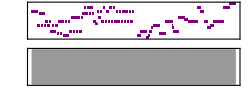

```mathematica
Clear[snd];
snd=Sound[{Sound[trebleClefBackwards,{0,whole*16}],Sound[bassClefBackwards,{0,whole*16}]}]
```

```mathematica
Export[{snd.mid},]
```